判断值=-34

状态改变时间=8.57143s

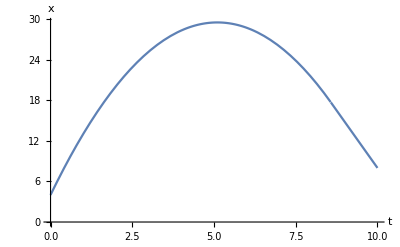

```mathematica
(*https://mp.weixin.qq.com/s?__biz=MzAwNTA5NTYxOA==&mid=2650868136&idx=4&sn=7dd9604c8f182a1806b3fb27465994ed&chksm=80d44005b7a3c913074e56b077adef7cb2508f3a3aed3ac4ec71299c5a072763182887ca18b8&mpshare=1&scene=1&srcid=0513RCYuwagpHd9x0REnmiAC&pass_ticket=nU4j9odakdSuPx81A2QstZhQIjgZiikSqfoYtdKlO%2FDV2%2B0MwWUSu9afUCNemqOR#rd*)
v0=10;w0=8;R=4;mu=0.2;g=9.8;
δ=(2 (v0+w0 R))/(5 mu g);
"判断值="<>ToString[3 v0-2 w0 R]
"状态改变时间="<>ToString[(2 (v0+w0 R))/(5 mu g)]<>"s"
location[t_]=Piecewise[{
{If[t≤δ,v0 t-1/2* mu*g*t^2+R,(3v0-2w0 R)/5(t-δ)+v0 δ-1/2* mu*g*δ^2+R],3 v0-2 w0 R<0},(*<0回滚*)
{If[t≤δ,v0 t-1/2* mu*g*t^2+R,v0 δ-1/2* mu*g*δ^2+R],3 v0-2 w0 R==0},
{If[t≤δ,v0 t-1/2* mu*g*t^2+R,(3v0-2w0 R)/5(t-δ)+v0 δ-1/2* mu*g*δ^2+R],3 v0-2 w0 R>0}
}];(*>0向前滚*)

Plot[location[t],{t,0,10},AxesOrigin->{0,0},AxesLabel->{t,x}]
zhuanjiao[t_]=If[t≤δ,w0 t-(3 mu g)/(4 R)t^2,w0 δ-(3 mu g)/(4 R)δ^2-(3v0-2w0 R)/(5R)(t-δ)];(*>0向前滚*)
(*Plot[zhuanjiao[t],{t,0,5},AxesOrigin->{0,0},AxesLabel->{t,w}]*)
Manipulate[
Graphics3D[
Rotate[Sphere[{location[t],R,R},R],-zhuanjiao[t],{0,1,0},{location[t],R,R}] ,Method->{"SpherePoints"->10},(*降低取样数来实现效果*)
Axes->True,AxesOrigin->{0,0,0},PlotRange->{{0,40},{0,2R},{0,2R}},AxesLabel->{x,y,z}
],{t,0,2(2 (v0+w0 R))/(5 mu g)+10}]
```